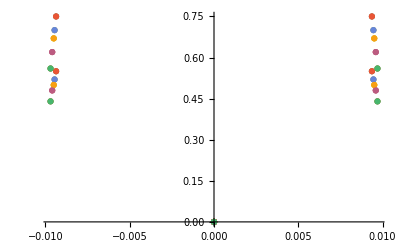

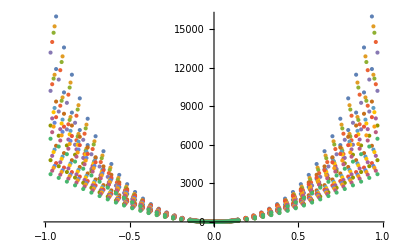

```mathematica
m={12.0107,91.224,1};
kB=1000*8.617332478*10^−5;K2meV=1000*8.617332478*10^−5;kjmol2evatom=1/(96.487*64);
e0perf={-.67382051*10^3,-.67479111*10^3,-.67540188*10^3,-.67568572*10^3,-.67550095*10^3,-.67441442*10^3,-.67323280*10^3,-.67090290*10^3,-.66733277*10^3};
volperf={766.060,778.688,791.453,808.70835,822.656,846.590,862.257,885.289,912.673};
(*Data in*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/allvols"];
filesC={"C_4685_760","C_4730_1900","C_4759_2500","C_4801_3200","C_4850_3805","C_4685_760_110","C_4730_1900_110","C_4759_2500_110","C_4801_3200_110","C_4850_3805_110","C_4685_760_111","C_4730_1900_111","C_4759_2500_111","C_4801_3200_111","C_4850_3805_111"};
filesZr={"Zr_4685_760","Zr_4730_1900","Zr_4759_2500","Zr_4801_3200","Zr_4850_3805","Zr_4685_760_110","Zr_4730_1900_110","Zr_4759_2500_110","Zr_4801_3200_110","Zr_4850_3805_110","Zr_4685_760_111","Zr_4730_1900_111","Zr_4759_2500_111","zr_4801_3200_111","Zr_4850_3805_111"};
filesCh={"1.harm.C_4685_760","1.harm.C_4730_1900","1.harm.C_4759_2500","1.harm.C_4801_3200","1.harm.C_4850_3805","1.harm.C_4685_760_110","1.harm.C_4730_1900_110","1.harm.C_4759_2500_110","1.harm.C_4801_3200_110","1.harm.C_4850_3805_110","1.harm.C_4685_760_111","1.harm.C_4730_1900_111","1.harm.C_4759_2500_111","1.harm.C_4801_3200_111","1.harm.C_4850_3805_111"};
filesZrh={"1.harm.Zr_4685_760","1.harm.Zr_4730_1900","1.harm.Zr_4759_2500","1.harm.Zr_4801_3200","1.harm.Zr_4850_3805","1.harm.Zr_4685_760_110","1.harm.Zr_4730_1900_110","1.harm.Zr_4759_2500_110","1.harm.Zr_4801_3200_110","1.harm.Zr_4850_3805_110","1.harm.Zr_4685_760_111","1.harm.Zr_4730_1900_111","1.harm.Zr_4759_2500_111","1.harm.Zr_4801_3200_111","1.harm.Zr_4850_3805_111"};
Cdata=Table[ReadList[filesC[[i]],{Number, Number}],{i,1,15}];
Zrdata=Table[ReadList[filesZr[[i]],{Number, Number}],{i,1,15}];
hCdata=Table[ReadList[filesCh[[i]],{Number, Number}],{i,1,15}];
hZrdata=Table[ReadList[filesZrh[[i]],{Number, Number}],{i,1,15}];
Show[ListPlot@hCdata,ListPlot@hZrdata,PlotRange->All]
Show[ListPlot@Cdata,ListPlot@Zrdata,PlotRange->All]
```

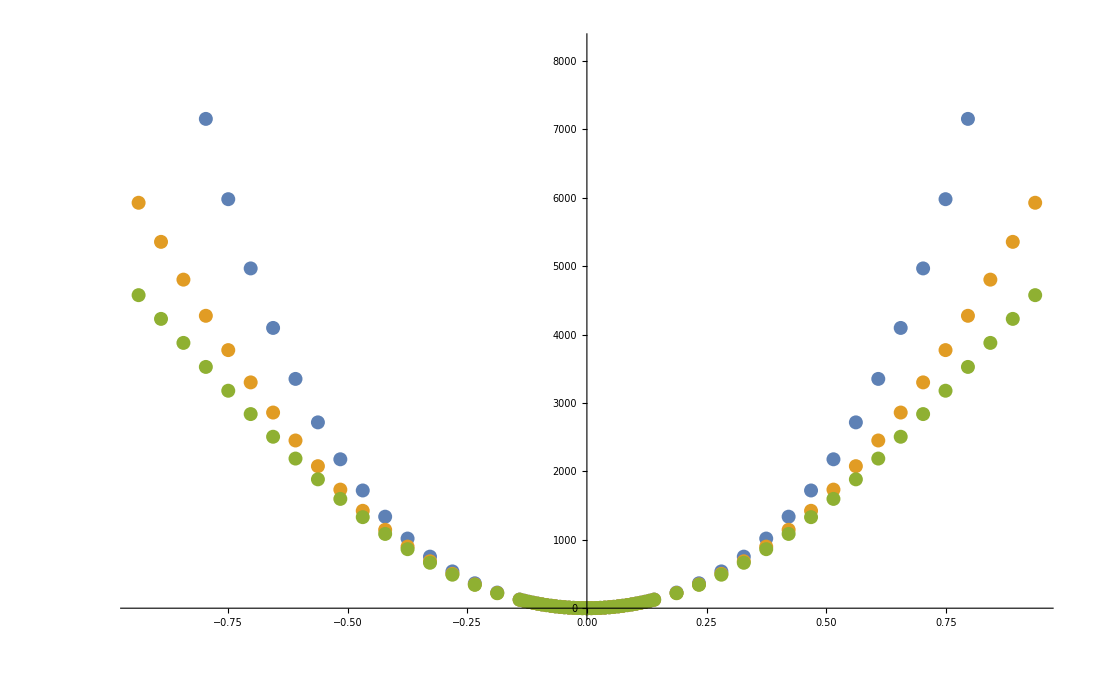

```mathematica
ListPlot[{Cdata[[1]],Cdata[[6]],Cdata[[11]],hCdata}]
```

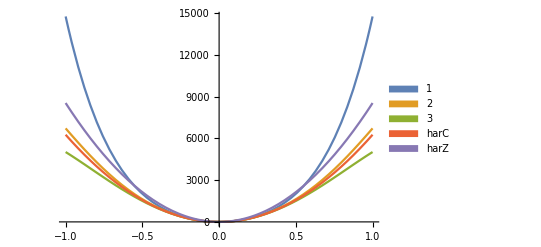

```mathematica
Plot[Evaluate@{V[1,6,x],V[1,2,x][[1]],V[2,2,x][[1]]},{x,-1,1},PlotLegends->SwatchLegend[{1,2,3,harC,harZ}]]
```

```mathematica
Define and fit potentials;
(*Carbon*)
V[1,2,x_]:=Table[Fit[hCdata[[i]],{x^2},x],{i,1,15}]
V[1,4,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4},x],{i,1,15,5}]
V[1,6,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6},x],{i,1,15,5}]
V[1,8,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,15,5}]
V[1,10,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,15,5}]
V[1,12,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,15}]

V[2,2,x_]:=Table[Fit[hZrdata[[i]],{x^2},x],{i,1,15}]
V[2,4,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4},x],{i,1,15,5}]
V[2,6,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6},x],{i,1,15,5}]
V[2,8,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,15,5}]
V[2,10,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,15,5}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,15}]
GraphicsGrid[{{Show[Plot[Evaluate@{V[1,2,x][[1]],V[1,12,x][[1]],V[1,12,x][[6]],V[1,12,x][[11]]},{x,-1.2,1.2},PlotLegends->SwatchLegend[{"harmonic","100 anharmonic","110 anharmonic","111 anharmonic"}],PlotLabel->"Carbon potentials at 4.685Angstrom",AxesLabel->{"Angstrom","meV/atom"}],ImageSize->500],Show[Plot[Evaluate@{V[2,2,x][[1]],V[2,12,x][[1]],V[2,12,x][[6]],V[2,12,x][[11]]},{x,-1.2,1.2},PlotLegends->SwatchLegend[{"harmonic","100 anharmonic","110 anharmonic","111 anharmonic"}],PlotLabel->"Zirconium potentials at 4.685Angstrom",AxesLabel->{"Angstrom","meV/atom"}],ImageSize->500]}},ImageSize->1300]
```

```mathematica
"Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Acarbon=Table[V[1,2,x][[i]][[1]],{i,1,1}]
"cOmega0 in meV/Ang**2/AMU is approximately"
cOmega0=Sqrt[2Acarbon/m[[1]]]
"Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Azirconium=Table[V[2,2,x][[i]][[1]],{i,1,1}]
"Z_Omega_0 in meV/Ang**2/AMU is approximately"
zOmega0=Sqrt[2Azirconium/m[[2]]]
```

Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

{6264.46}

cOmega0 in meV/Ang**2/AMU is approximately

{32.2978}

Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

{8542.44}

Z_Omega_0 in meV/Ang**2/AMU is approximately

{13.6852}

```mathematica
Carbon and zirconium - calculate eigenvalues and vectors;
(*Find the first x eigenvalues and eigenvectors*)
Neigenvalues=300;
(*Define bounds for plotting and solving eigenproblem*)
B=1.2;H=2000;
(*Carbon Hamiltonians - from harmonic, even symmetry to 12th order*)
ℒallc=Table[-(1/(2m[[1]]))*u''[x]+V[1,i,x]*u[x],{i,2,12,10}];
(*Zirconium Hamiltonians - harmonic, even symmetry to 12th order*)
ℒallz=Table[-(1/(2m[[2]]))*u''[x]+V[2,i,x]*u[x],{i,2,12,10}];
solverOptions={Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}};
```

```mathematica
(*ℒallc[[1=harmonic]]ℒallc[[2=anharmonic 12th order]]*)
ℒallc;
```

```mathematica
(*char1d=Table[NDEigensystem[ℒallc[[1]][[i]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{i,1,15}];
canh1d=Table[NDEigensystem[ℒallc[[2]][[i]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{i,1,15}];*)
```

```mathematica
(*zhar1d=Table[NDEigensystem[ℒallz[[1]][[i]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{i,1,15}];
zanh1d=Table[NDEigensystem[ℒallz[[2]][[i]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{i,1,15}];*)
```

```mathematica
(*DumpSave["dump.char1d.mx",char1d]*)
```

{{1}}
 |  |  |  |

```mathematica
(*DumpSave["dump.canh1d.mx",canh1d]
DumpSave["dump.zhar1d.mx",zhar1d]
DumpSave["dump.zanh1d.mx",zanh1d]*)
```

{{1}}
 |  |  |  |

{{{{6.84261,20.5278,34.213,47.8982,61.5834,75.2687,288,4030.35,4044.04,4057.72,4071.41,4085.1,4098.78},{1}},13,{1}}}
 |  |  |  |

{{{{6.87947,20.6461,34.4281,48.2255,62.0382,75.8663,288,4648.53,4666.13,4683.74,4701.36,4718.99,4736.63},{1}},13,{1}}}
 |  |  |  |

```mathematica
Get["dump.char1d.mx"]
Get["dump.canh1d.mx"]
Get["dump.zhar1d.mx"]
Get["dump.zanh1d.mx"]
```

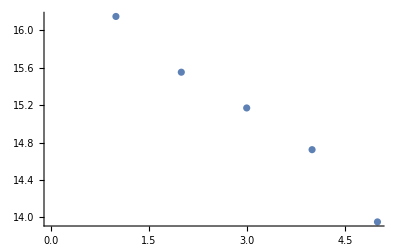

```mathematica
ListPlot@Table[char1d[[i]][[1]][[1]],{i,1,5}]
```

```mathematica
(*NOTE also rescale the anharmonic frequencies to tend exactly to the harmonic freqs in the limit of low T ie the first mode*)
(*... there is a small random error 0.05% at for omega0, but over 200 eigenvalues gets amplied so messes up volume order of distributions*)
(*Exmaple:*)
canh1d[[1]][[1]][[1;;20]]
canh1d[[1]][[1]][[1;;20]]/canh1d[[1]][[1]][[1]]
char1d[[1]][[1]][[1]]*canh1d[[1]][[1]][[1;;20]]/canh1d[[1]][[1]][[1]]
```

{16.1757,48.5936,81.1442,113.826,146.639,179.582,212.654,245.854,279.181,312.634,346.213,379.916,413.744,447.694,481.767,515.961,550.276,584.711,619.266,653.938}

{1.,3.00411,5.01643,7.03688,9.06541,11.102,13.1465,15.199,17.2593,19.3274,21.4033,23.4869,25.5781,27.677,29.7834,31.8973,34.0187,36.1475,38.2837,40.4272}

{16.1489,48.5131,81.0097,113.638,146.396,179.285,212.301,245.446,278.718,312.116,345.639,379.287,413.058,446.952,480.968,515.106,549.364,583.742,618.239,652.855}

```mathematica
maxval=250;
(*Fix harmonic to use perfect summation from omega0*)
(*char1de=Table[char1d[[i]][[1]][[1]],{i,1,15}];*)
(*canh1de=Table[canh1d[[i]][[1]][[1;;maxval]],{i,1,15}];*)
(*zhar1de=Table[zhar1d[[i]][[1]][[1;;maxval]],{i,1,15}];*)
(*zanh1de=Table[zanh1d[[i]][[1]][[1;;maxval]],{i,1,15}];*)
char1de=Table[Table[char1d[[i]][[1]][[1]]*2(j-0.5),{j,1,maxval}],{i,1,15}];
canh1de=Table[char1d[[i]][[1]][[1]]*canh1d[[i]][[1]][[1;;maxval]]/canh1d[[i]][[1]][[1]],{i,1,15}];
zhar1de=Table[Table[zhar1d[[i]][[1]][[1]]*2(j-0.5),{j,1,maxval}],{i,1,15}];
zanh1de=Table[zhar1d[[i]][[1]][[1]]*zanh1d[[i]][[1]][[1;;maxval]]/zanh1d[[i]][[1]][[1]],{i,1,15}];
```

```mathematica
Length[zanh1de[[15]]]
```

250

```mathematica
char1d[[1]][[1]][[1]]
```

16.1489

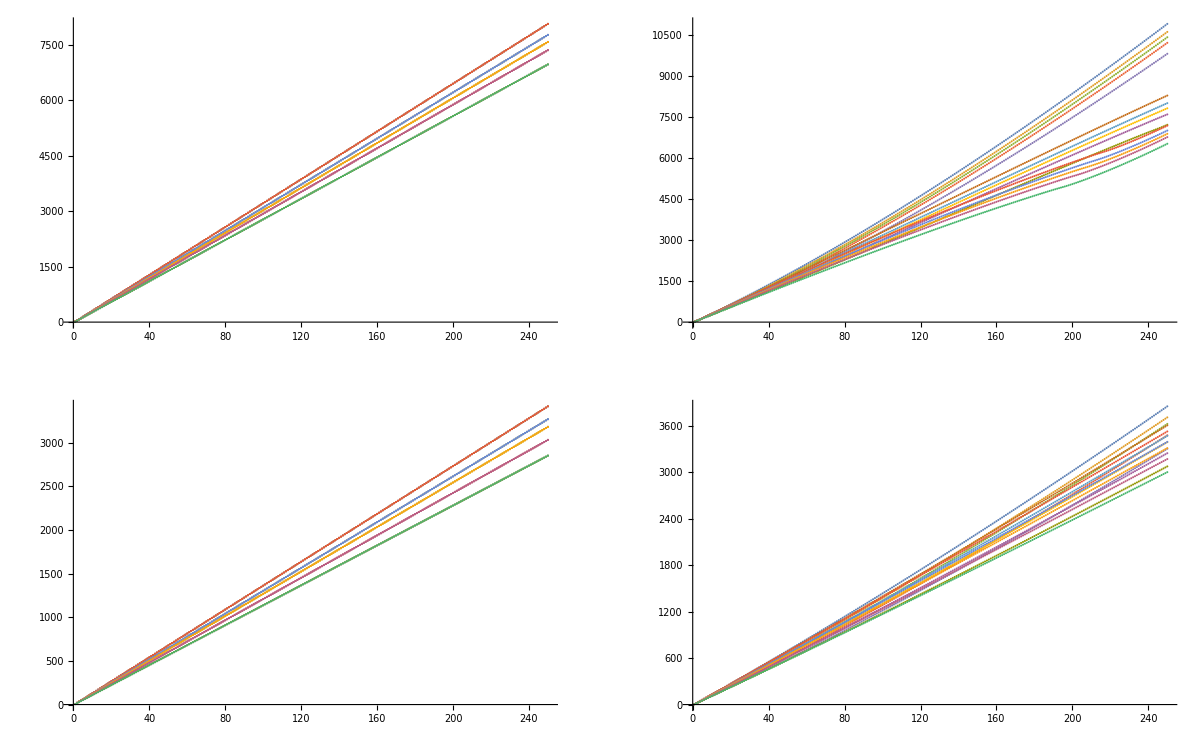

```mathematica
GraphicsGrid[{{ListPlot[char1de],ListPlot[canh1de[[1;;15]]]},{ListPlot[zhar1de],ListPlot[zanh1de[[1;;15]]]}},ImageSize->1200]
```

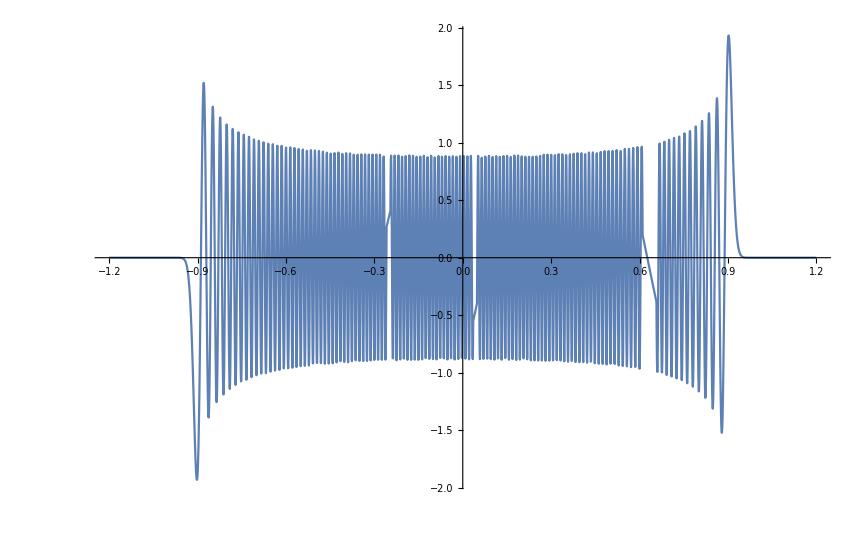

```mathematica
Plot[canh1d[[1]][[2]][[250]],{x,-1.2,1.2}]
```

```mathematica
(*Repeated of above WITH 400 EIGENVALUES*)
(*Table[2*16.148887026360963(i+0.5),{i,0,300,1}]*)
GraphicsGrid[{Table[Show[ListPlot[char1de[[i]],PlotStyle->{Red},PlotLegends->SwatchLegend[{"Harmonic"}],ImageSize->400],ListPlot[{canh1de[[i]],canh1de[[5+i]],canh1de[[10+i]]},PlotLegends->SwatchLegend[{"Zr 001 anharmonic","Zr 011 anharmonic","Zr 111 anharmonic"}]]],{i,1,5}]},ImageSize->3000]
```

-Graphics-

```mathematica
GraphicsGrid[{Table[ListPlot[{canh1de[[i]]/char1de[[i]],canh1de[[5+i]]/char1de[[i]],canh1de[[10+i]]/char1de[[i]]},ImageSize->400,PlotLegends->SwatchLegend[{"Zr 001 anharmonic","Zr 011 anharmonic","Zr 111 anharmonic"}]],{i,1,5}]},ImageSize->3000]
```

-Graphics-

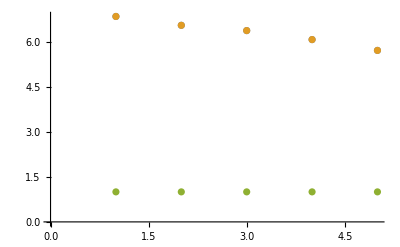

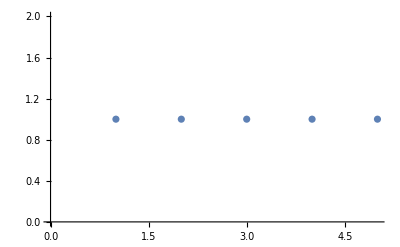

```mathematica
ListPlot[{Table[zanh1de[[i]][[1]],{i,1,5}],Table[zhar1de[[i]][[1]],{i,1,5}],Table[zanh1de[[i]][[1]],{i,1,5}]/Table[zhar1de[[i]][[1]],{i,1,5}]}]
ListPlot[{Table[zanh1de[[i]][[1]],{i,1,5}]/Table[zhar1de[[i]][[1]],{i,1,5}]}]
```

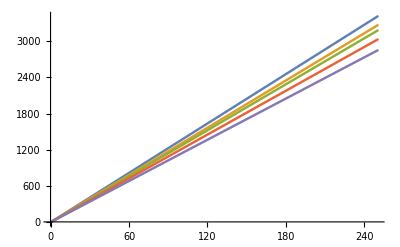

```mathematica
ListPlot[Evaluate@zhar1de[[1;;5]],PlotLegends->SwatchLegend["1","2","3","4","5"]]
```

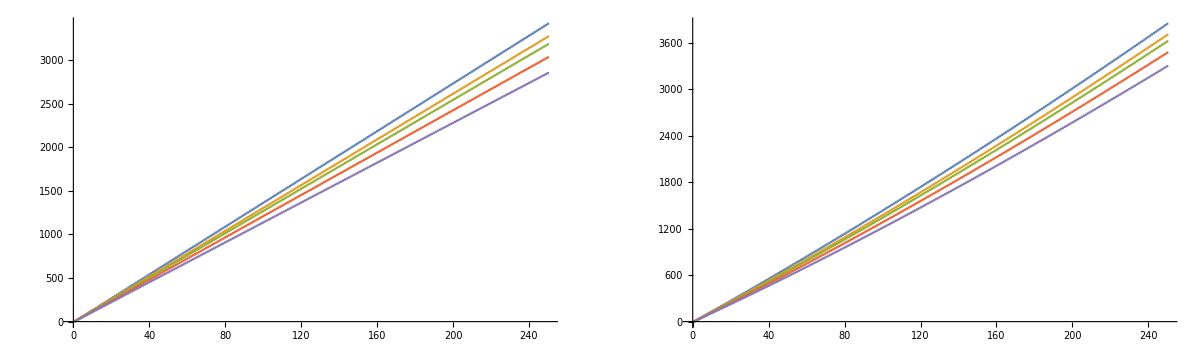

```mathematica
GraphicsGrid[{{ListPlot[zhar1de[[1;;5]],PlotLegends->SwatchLegend["1","2","3","4","5"]],ListPlot[zanh1de[[1;;5]]]}},ImageSize->1200]
```

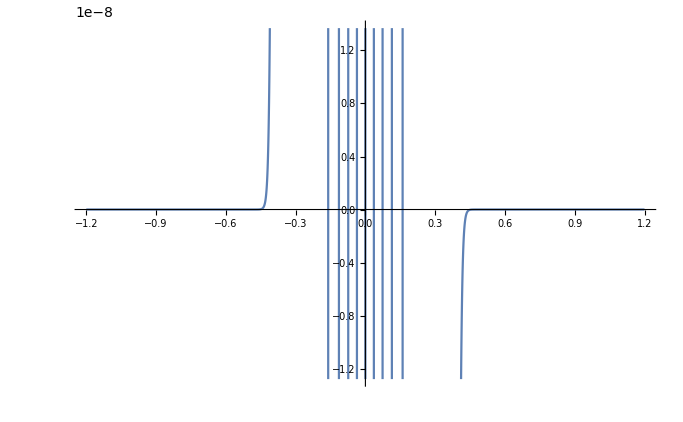

```mathematica
Plot[canh1d[[1]][[2]][[10]],{x,-1.2,1.2}]
```

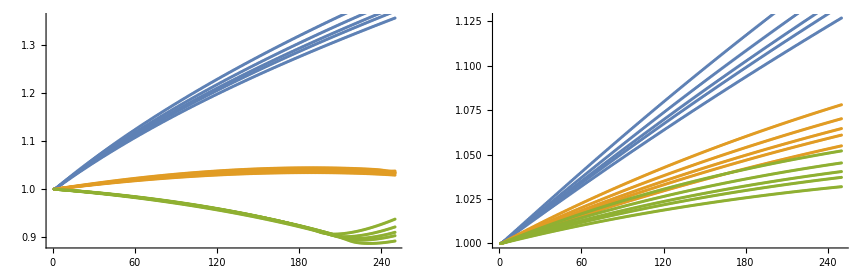

```mathematica
GraphicsGrid[{{Show@Table[ListPlot[{canh1de[[i]]/char1de[[i]],canh1de[[5+i]]/char1de[[i]],canh1de[[10+i]]/char1de[[i]]},ImageSize->400],{i,1,5}],Show@Table[ListPlot[{zanh1de[[i]]/zhar1de[[i]],zanh1de[[5+i]]/zhar1de[[i]],zanh1de[[10+i]]/zhar1de[[i]]},ImageSize->400],{i,1,5}]}}]
```

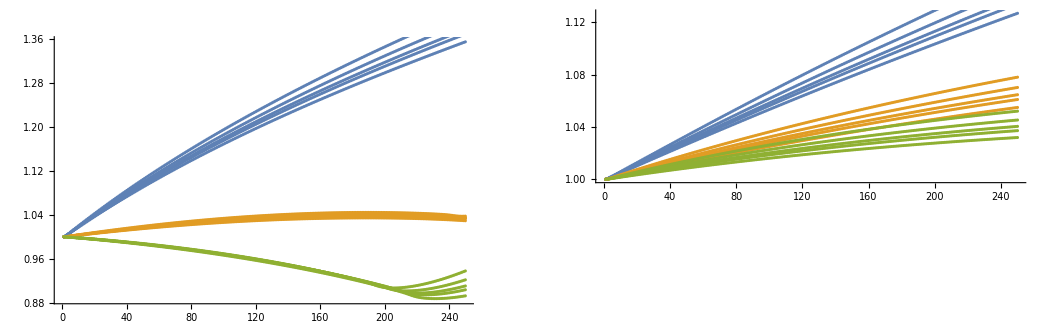

```mathematica
fr[T_,spectrumZ_,spectrumC_,maxEigen_,xFactor_,pFactor_]:=-K2meV*(pFactor)*T*Log[{Total[Exp[-xFactor*spectrumZ/(K2meV*T)]],Total[Exp[-xFactor*spectrumC/(K2meV*T)]]}]
```

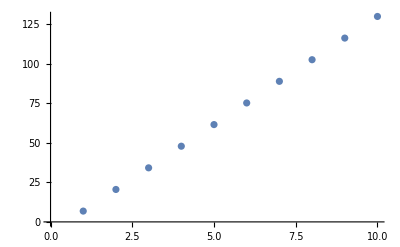

-6.84261+13.6852 x-3.22455×10^-15 x^2+4.16141×10^-17 x^3-2.71353×10^-19 x^4+8.62231×10^-22 x^5-1.07861×10^-24 x^6

```mathematica
ListPlot@zhar1de[[1]][[1;;10]]
Fit[zhar1de[[1]],Table[x^i,{i,0,6}],x]
```

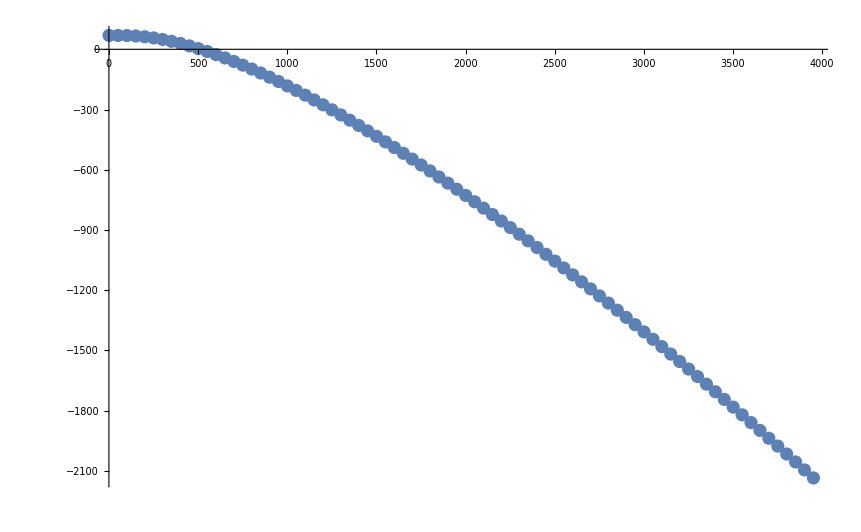

```mathematica
ListPlot[Table[{t,Total@fr[t,zhar1de[[1]],char1de[[1]],50,2,1.5]},{t,1,4000,50}]]
```

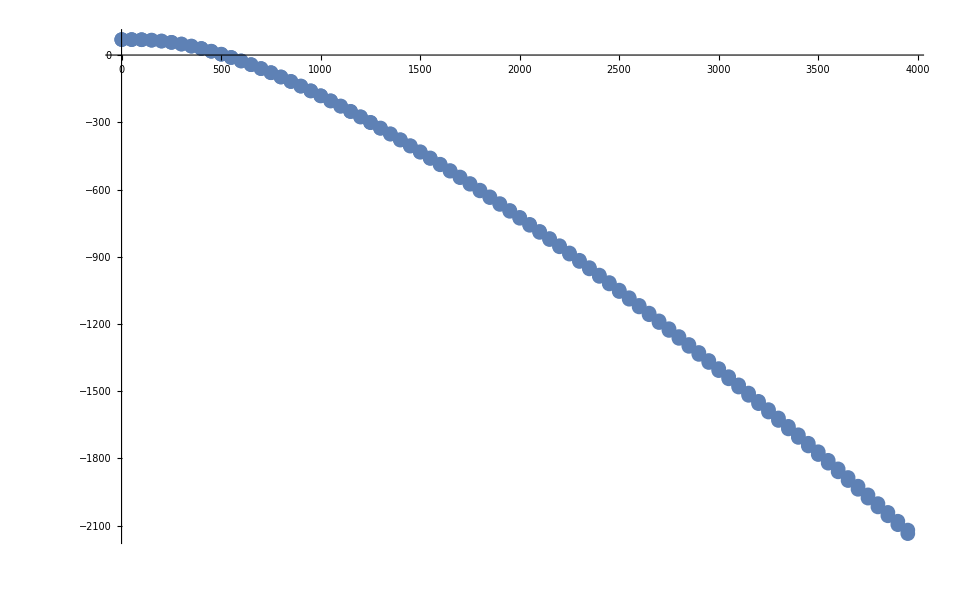

{4.685Å⟨001⟩,4.685Å⟨011⟩,4.685Å⟨111⟩,4.730Å⟨001⟩,4.730Å⟨011⟩,4.730Å⟨111⟩,4.759Å⟨001⟩,4.759Å⟨011⟩,4.759Å⟨111⟩,4.801Å⟨001⟩,4.801Å⟨011⟩,4.801Å⟨111⟩,4.850Å⟨001⟩,4.850Å⟨011⟩,4.850Å⟨111⟩}

```mathematica
Show[ListPlot[Table[{t,Total@fr[t,zhar1de[[1]],char1de[[1]],50,2,1.5]},{t,1,4000,50}]],ListPlot[Table[{t,Total@fr[t,zanh1de[[1]],canh1de[[1]],150,2,1.5]},{t,1,4000,50}]]]
```

{4.685Å ⟨001⟩,4.730Å ⟨001⟩,4.759Å ⟨001⟩,4.801Å ⟨001⟩,4.850Å ⟨001⟩,4.685Å ⟨011⟩,4.730Å ⟨011⟩,4.759Å ⟨011⟩,4.801Å ⟨011⟩,4.850Å ⟨011⟩,4.685Å ⟨111⟩,4.730Å ⟨111⟩,4.759Å ⟨111⟩,4.801Å ⟨111⟩,4.850Å ⟨111⟩}

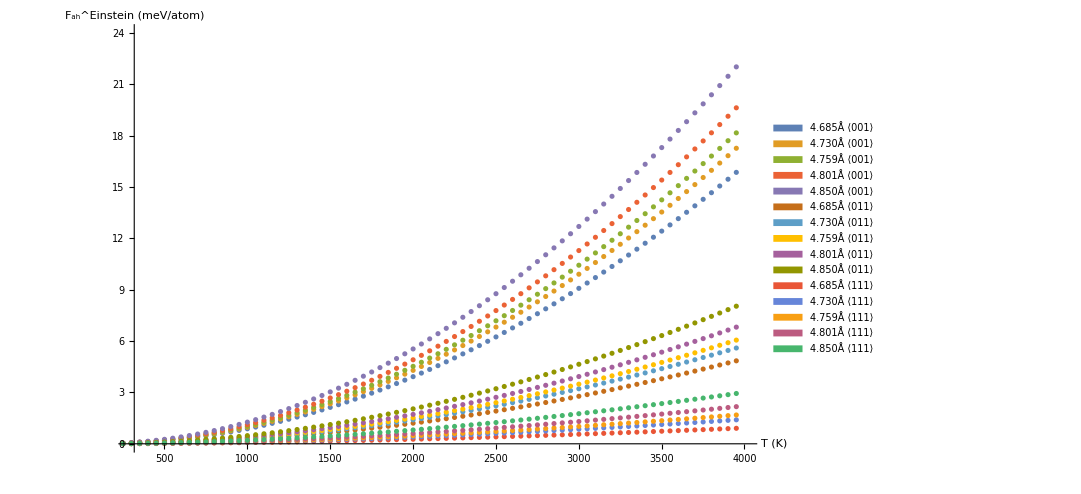

```mathematica
vols={"4.685Å","4.730Å","4.759Å","4.801Å","4.850Å"};
dirs={" ⟨001⟩"," ⟨011⟩"," ⟨111⟩"};
plab=Flatten@Table[StringJoin[vols[[i]],dirs[[j]]],{j,1,3},{i,1,5}]
ListPlot[Table[Table[{t,Total@fr[t,zanh1de[[i]],canh1de[[i]],150,2,1.5]-Total@fr[t,zhar1de[[i]],char1de[[i]],150,2,1.5]},{t,1,4000,50}],{i,1,15}],PlotRange->{{minT,maxT},{0,24}},PlotLegends->SwatchLegend[plab],ImageSize->800,AxesLabel->{"T (K)","F_ah^Einstein (meV/atom)"},PlotStyle->"Thick"]
```

```mathematica
1
```

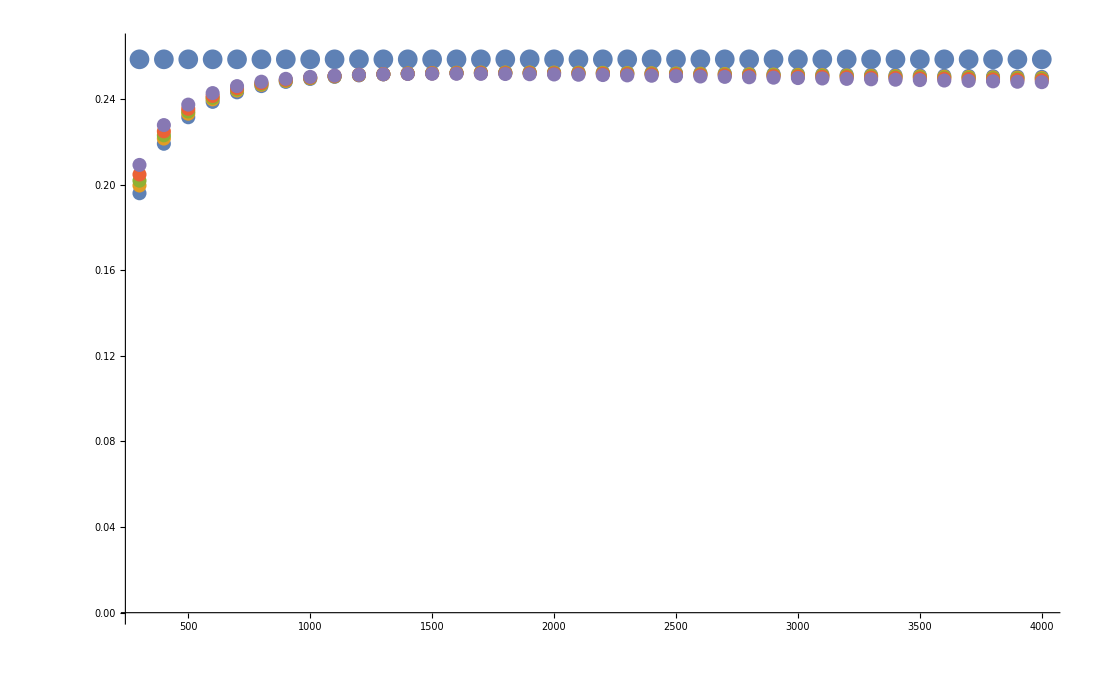

```mathematica
dT=100;
maxT=4000;
minT=300;
Show[ListPlot[Table[{T,3kB},{T,minT,maxT,dT}],PlotRange->{All,{0,0.265}}],ListPlot[Table[ Table[{T,t*D[-D[Total@fr[t,zanh1de[[vol]],canh1de[[vol]],150,2,1.5],t],t]}/.t->T,{T,minT,maxT,dT}],{vol,1,5}]]]
```

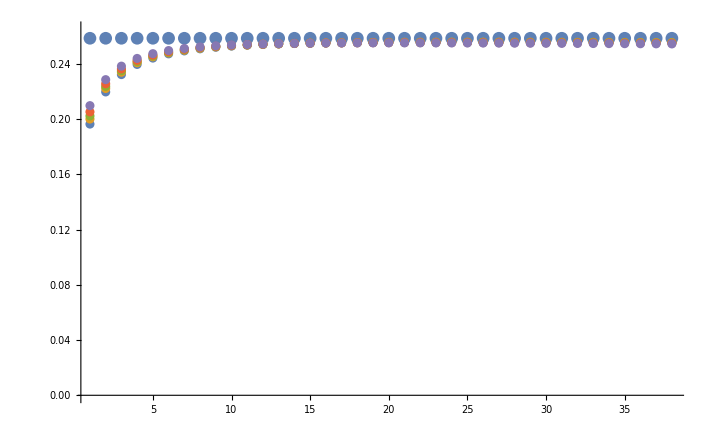

```mathematica
Show[ListPlot[Table[3kB,{T,minT,maxT,dT}],PlotRange->{All,{0,0.265}}],ListPlot[Table[ Table[t*D[-D[Total@fr[t,zanh1de[[vol]],canh1de[[vol]],150,2,1.5],t],t]/.t->T,{T,minT,maxT,dT}],{vol,6,10}]]]
```

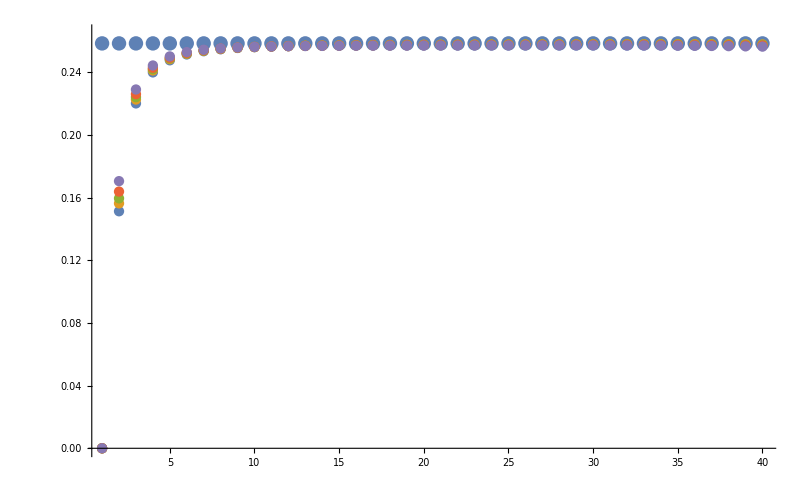

```mathematica
Show[ListPlot[Table[3kB,{T,minT,maxT,dT}],PlotRange->{All,{0,0.265}}],ListPlot[Table[ Table[t*D[-D[Total@fr[t,zanh1de[[vol]],canh1de[[vol]],1,250],t],t]/.t->T,{T,minT,maxT,dT}],{vol,11,15}]]]
```

825.578-4.8031 x+0.00499217 x^2-1.66738×10^-6 x^3

20668.2-12550.3 x+2437.56 x^2-156.059 x^3

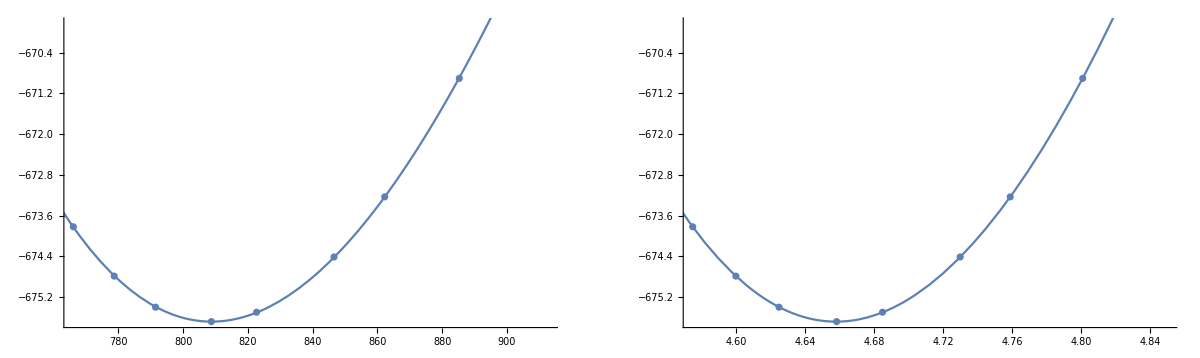

```mathematica
e0volfit=Fit[Transpose[{volperf,e0perf}],{1,x,x*x,x*x*x},x];
e0afit=Fit[Transpose[{0.5(volperf^(1/3)),e0perf}],{1,x,x*x,x*x*x},x];
e0volfit
e0afit
GraphicsGrid[{{Show[ListPlot[Transpose[{volperf,e0perf}]],Plot[e0volfit,{x,750,900}]],Show[ListPlot[Transpose[{0.5(volperf^(1/3)),e0perf}]],Plot[e0afit,{x,4.5,4.9}]]}},ImageSize->1200]
```

```mathematica
Minimize[e0afit,x]
(*Vinet perf min vol = 808.486847 and minE = -675.685917*)
vinetE=-675.685917
vinetvol=808.486847^(1/3)*0.5
e0perf[[4]]
```

{-675.686,{x→4.6581}}

-675.686

4.65794

-675.686

```mathematica
e0perf[[1;;9]]-e0perf[[4]]
```

{1.86521,0.89461,0.28384,0.,0.18477,1.2713,2.45292,4.78282,8.35295}

{1.86521,0.89461,0.28384,0.,0.18477,1.2713,2.45292,4.78282,8.35295}

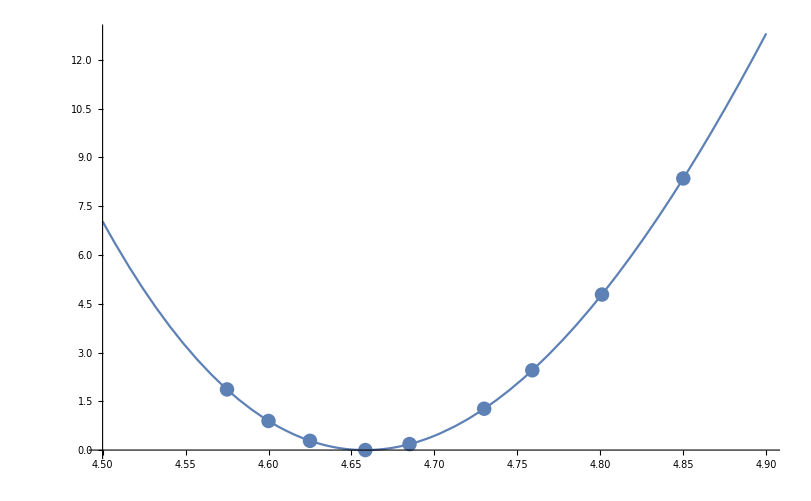

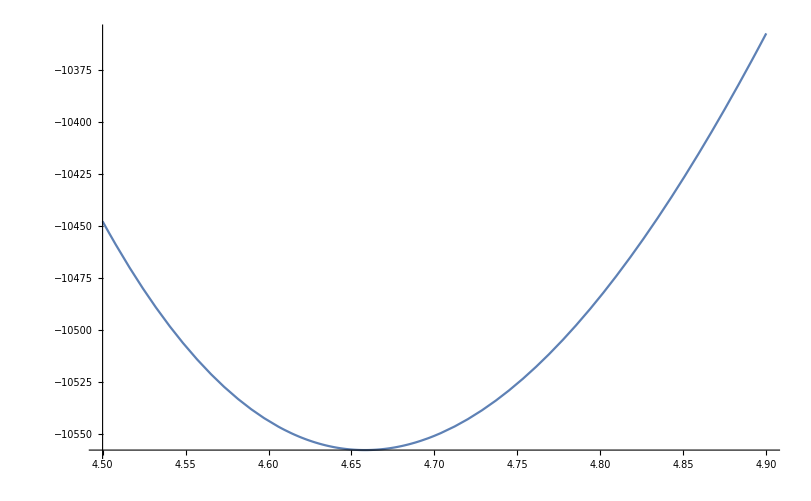

```mathematica
e0=e0perf[[1;;9]]-e0perf[[4]]
Show[Plot[Evaluate@Fit[Transpose[{a0,e0}],{1,x,x*x,x*x*x},x],{x,4.5,4.9}],ListPlot[Transpose[{a0,e0}]]]
Plot[e0afit*1000/64,{x,4.5,4.9}]
```

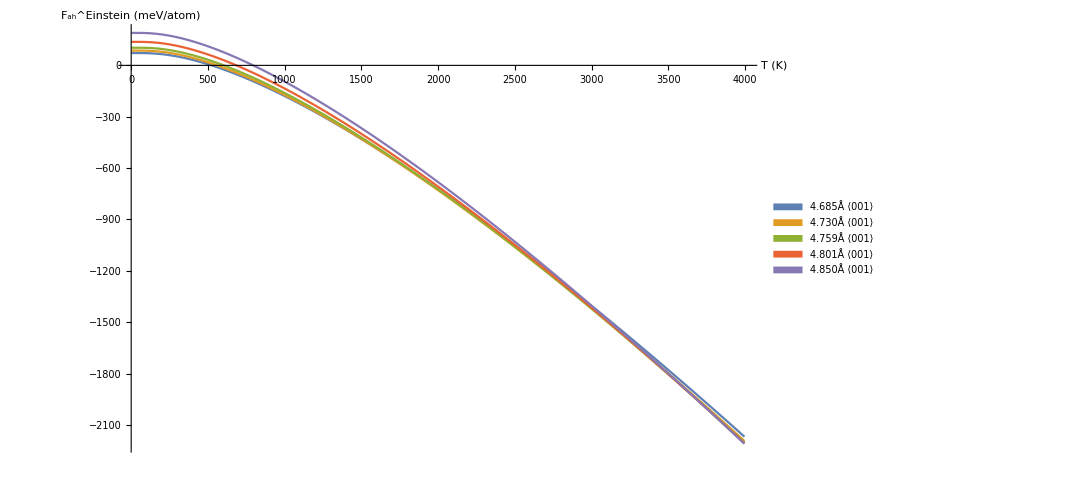

```mathematica
ListLinePlot[Table[Table[{t,1000/64*e0[[i]]+Total@fr[t,zhar1de[[i]],char1de[[i]],250,2,1.5]},{t,1,4000,5}],{i,1,5}],PlotLegends->SwatchLegend[plab],ImageSize->800,AxesLabel->{"T (K)","F_ah^Einstein (meV/atom)"},PlotStyle->PointSize[0.2]]
```

```mathematica
a0=0.5(volperf^(1/3))[[1;;9]]
Table[{a0[[i]],1000/64*e0[[i]]+Total@fr[t,zhar1de[[i]],char1de[[i]],250,2,1.5]},{i,1,5}]/.t->{1,50,500}
```

{4.575,4.6,4.625,4.65837,4.685,4.73,4.759,4.801,4.85}

{{4.575,{98.1184,98.1071,33.0149}},{4.6,{80.2801,80.2652,12.0571}},{4.625,{69.0636,69.0461,-1.1665}},{4.65837,{62.3915,62.3684,-11.0305}},{4.685,{61.8795,61.8472,-16.1814}}}

1.45122×10^6-920627. x+194659. x^2-13717.8 x^3

{-675.686,{x→4.6581}}

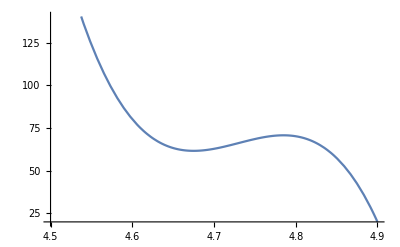

{38.6308,{x→4.88}}

-Graphics-

```mathematica
fit=Fit[Table[{a0[[i]],1000/64*e0[[i]]+Total@fr[t,zhar1de[[i]],char1de[[i]],250,2,1.5]},{i,1,5}]/.t->0.1,{1,x,x*x,x*x*x},x]
Minimize[e0afit,x]
Plot[fit,{x,4.5,4.9}]
Minimize[{fit,4.5<x<4.88},x]
Plot[fit,{x,4.5,4.9}]
```

```mathematica
temps[t_]:=1+9.7t^2
tlist=Table[temps[t],{t,0,20}]
fitT=Table[Fit[Table[{a0[[i]],1000/64*e0[[i]]+Total@fr[t,zhar1de[[i]],char1de[[i]],250,2,1.5]},{i,1,5}]/.t->tlist[[j]],{1,x,x*x,x*x*x},x],{j,1,21}];
fitTanh=Table[Fit[Table[{a0[[i]],1000/64*e0[[i]]+Total@fr[t,zanh1de[[i]],canh1de[[i]],250,2,1.5]},{i,1,5}]/.t->tlist[[j]],{1,x,x*x,x*x*x},x],{j,1,21}];
```

{1.,10.7,39.8,88.3,156.2,243.5,350.2,476.3,621.8,786.7,971.,1174.7,1397.8,1640.3,1902.2,2183.5,2484.2,2804.3,3143.8,3502.7,3881.}

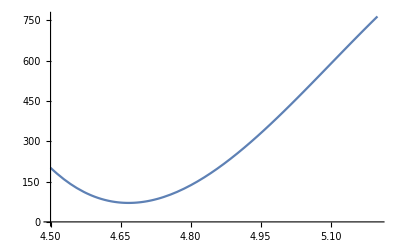

```mathematica
Plot[fitT[[1]],{x,4.5,5.2}]
```

```mathematica
minaData=Table[Minimize[{fitT[[i]],4.6<x<4.81},x],{i,1,21}]
minaDataanh=Table[Minimize[{fitTanh[[i]],4.6<x<4.81},x],{i,1,21}]
```

{{70.5753,{x→4.6672}},{70.5753,{x→4.6672}},{70.5737,{x→4.6672}},{70.2751,{x→4.66733}},{67.692,{x→4.66802}},{59.4537,{x→4.66962}},{42.124,{x→4.67219}},{12.8688,{x→4.67563}},{-30.505,{x→4.67978}},{-89.7381,{x→4.68453}},{-166.274,{x→4.68982}},{-261.358,{x→4.69562}},{-376.091,{x→4.70192}},{-511.473,{x→4.70875}},{-668.426,{x→4.71618}},{-847.813,{x→4.72435}},{-1050.46,{x→4.73349}},{-1277.19,{x→4.74404}},{-1528.83,{x→4.75692}},{-1806.37,{x→4.77491}},{-2111.67,{x→4.81}}}

{{70.5753,{x→4.6672}},{70.5753,{x→4.6672}},{70.5738,{x→4.6672}},{70.2758,{x→4.66733}},{67.6977,{x→4.66802}},{59.4778,{x→4.6696}},{42.1912,{x→4.67217}},{13.0183,{x→4.67558}},{-30.2161,{x→4.67968}},{-89.2313,{x→4.68438}},{-165.447,{x→4.68959}},{-260.078,{x→4.69528}},{-374.196,{x→4.70144}},{-508.766,{x→4.70809}},{-664.668,{x→4.71528}},{-842.722,{x→4.72313}},{-1043.7,{x→4.73182}},{-1268.36,{x→4.74167}},{-1517.45,{x→4.75336}},{-1791.79,{x→4.76852}},{-2092.53,{x→4.79527}}}

```mathematica
minA=Table[minaData[[i]][[2]][[1]][[2]],{i,1,21}]
mine0=Table[minaData[[i]][[1]],{i,1,21}]
minAanh=Table[minaDataanh[[i]][[2]][[1]][[2]],{i,1,21}]
mine0anh=Table[minaDataanh[[i]][[1]],{i,1,21}]
```

{4.6672,4.6672,4.6672,4.66733,4.66802,4.66962,4.67219,4.67563,4.67978,4.68453,4.68982,4.69562,4.70192,4.70875,4.71618,4.72435,4.73349,4.74404,4.75692,4.77491,4.81}

{70.5753,70.5753,70.5737,70.2751,67.692,59.4537,42.124,12.8688,-30.505,-89.7381,-166.274,-261.358,-376.091,-511.473,-668.426,-847.813,-1050.46,-1277.19,-1528.83,-1806.37,-2111.67}

{4.6672,4.6672,4.6672,4.66733,4.66802,4.6696,4.67217,4.67558,4.67968,4.68438,4.68959,4.69528,4.70144,4.70809,4.71528,4.72313,4.73182,4.74167,4.75336,4.76852,4.79527}

{70.5753,70.5753,70.5738,70.2758,67.6977,59.4778,42.1912,13.0183,-30.2161,-89.2313,-165.447,-260.078,-374.196,-508.766,-664.668,-842.722,-1043.7,-1268.36,-1517.45,-1791.79,-2092.53}

```mathematica
grunHar=ListPlot@Transpose[{minA,mine0}];
grunAnh=ListPlot@Transpose[{minAanh,mine0anh}];
```

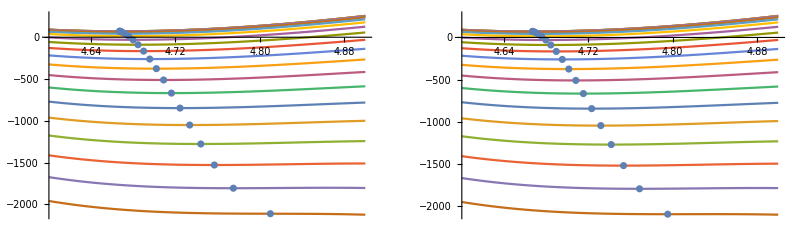

```mathematica
GraphicsGrid[{{Show[Plot[fitT,{x,4.6,4.9}],grunHar],Show[Plot[fitTanh,{x,4.6,4.9}],grunAnh]}},ImageSize->800]
```

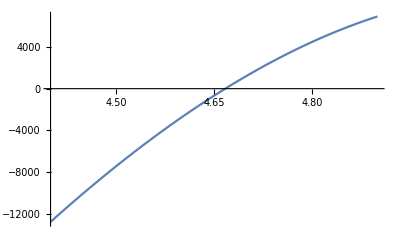

{-0.00129717,-0.00172268,-0.000180363,0.00140124,-0.00318847,0.0025027,-0.0012087,-0.00623518,0.,-0.00588709,-0.00978026,-0.0065065,-0.00601964,0.00805302,0.00222518,-0.000768687,-2.82799×10^-6,0.,-0.00377614,-0.0103498,-107.622}

4.6672

```mathematica
(*Maxwell identity:
G(T)=F(V,T)-V*dF/dV
http://www.tandfonline.com/doi/pdf/10.1080/01418638108222168?needAccess=true  J Harding paper
*)
Plot[Evaluate[x*D[fitT[[1]],x]],{x,4.4,4.9}]
Table[Evaluate[x*D[fitT[[i]],x]]/.x->minA[[i]],{i,1,21}]
minA[[1]]
```

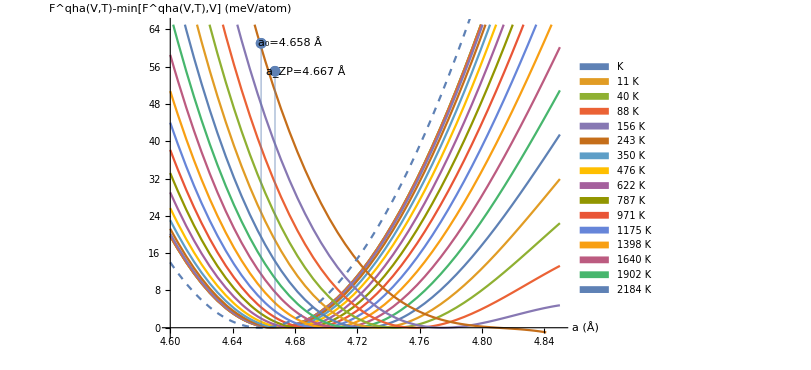

```mathematica
Show[Plot[Evaluate[fitT-mine0],{x,4.6,4.85},PlotLegends->SwatchLegend[Round[tlist]"K"],PlotRange->{Automatic,{-1,65}},AxesLabel->{"a (Å)","F^qha(V,T)-min[F^qha(V,T),V]\n (meV/atom)"},ImageSize->600],ListPlot[{{4.6583,61}},Filling->Bottom],Graphics[{Text["a_0=4.658 Å",{4.677,61}]}],ListPlot[{{4.6672,55}},Filling->Bottom],Graphics[{Text["a_ZP=4.667 Å",{4.687,55}]}],Plot[Evaluate[(e0afit-Minimize[e0afit,x][[1]])*1000/64],{x,4.6,4.85},PlotStyle->Dashed,PlotLegends->{"E_0(V)"}]]
```

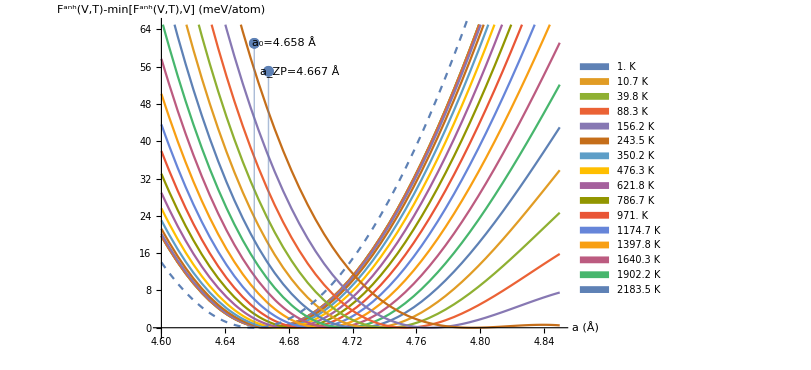

```mathematica
Show[Plot[Evaluate[fitTanh-mine0anh],{x,4.6,4.85},PlotLegends->SwatchLegend[tlist"K"],PlotRange->{Automatic,{-1,65}},AxesLabel->{"a (Å)","F^anh(V,T)-min[F^anh(V,T),V]\n (meV/atom)"},ImageSize->600],ListPlot[{{4.6583,61}},Filling->Bottom],Graphics[{Text["a_0=4.658 Å",{4.677,61}]}],ListPlot[{{4.6672,55}},Filling->Bottom],Graphics[{Text["a_ZP=4.667 Å",{4.687,55}]}],Plot[Evaluate[(e0afit-Minimize[e0afit,x][[1]])*1000/64],{x,4.6,4.85},PlotStyle->Dashed,PlotLegends->{"E_0(V)"}]]
```

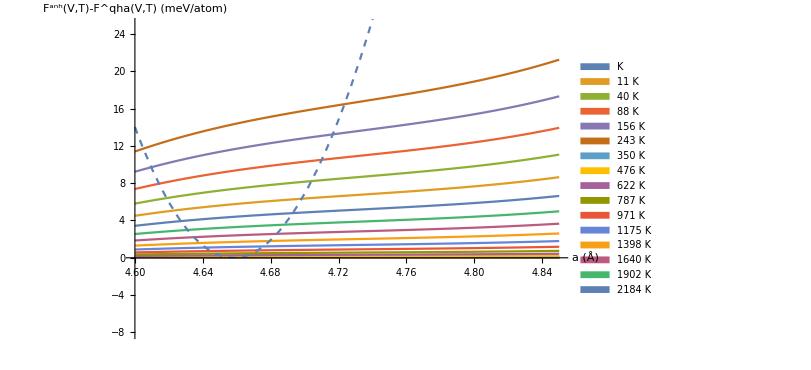

```mathematica
Show[Plot[Evaluate[(fitTanh)-(fitT)],{x,4.6,4.85},PlotLegends->SwatchLegend[Round[tlist]"K"],PlotRange->{Automatic,{-8,25}},AxesLabel->{"a (Å)","F^anh(V,T)-F^qha(V,T)\n (meV/atom)"},ImageSize->600],Plot[Evaluate[(e0afit-Minimize[e0afit,x][[1]])*1000/64],{x,4.6,4.85},PlotStyle->Dashed,PlotLegends->{"E_0(V)"}]]
```

```mathematica
mine0anh
```

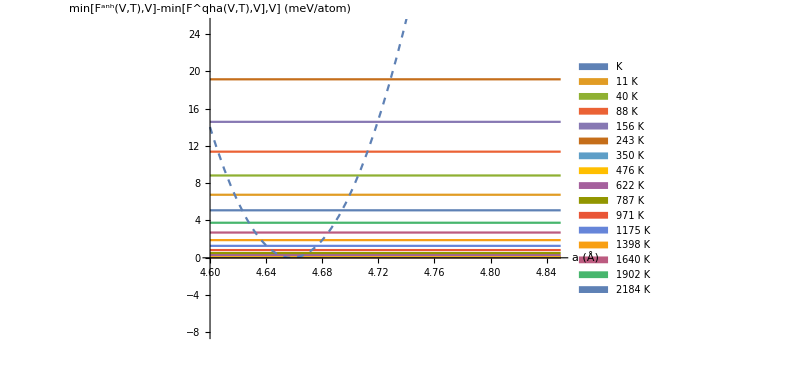

```mathematica
Show[Plot[Evaluate[(mine0anh)-(mine0)],{x,4.6,4.85},PlotLegends->SwatchLegend[Round[tlist]"K"],PlotRange->{Automatic,{-8,25}},AxesLabel->{"a (Å)","min[F^anh(V,T),V]-min[F^qha(V,T),V],V]\n (meV/atom)"},ImageSize->600],Plot[Evaluate[(e0afit-Minimize[e0afit,x][[1]])*1000/64],{x,4.6,4.85},PlotStyle->Dashed,PlotLegends->{"E_0(V)"}]]
```

```mathematica
tmax=4010;
tlistall=Table[t,{t,1,tmax}];
fitTall=Table[Fit[Table[{a0[[i]],1000/64*e0[[i]]+Total@fr[t,zhar1de[[i]],char1de[[i]],250,2,1.5]},{i,1,5}]/.t->T,{1,x,x*x,x*x*x},x],{T,1,tmax}];
```

```mathematica
Plot[fitTall[[1]],{x,4.5,5.2}]
```

-Graphics-

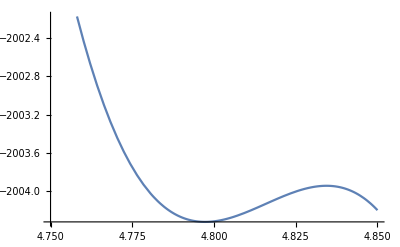

```mathematica
Plot[fitTall[[3750]],{x,4.75,4.85}]
```

```mathematica
interTall=Table[Interpolation[Table[{a0[[i]],1000/64*e0[[i]]+Total@fr[t,zhar1de[[i]],char1de[[i]],250,2,1.5]},{i,1,5}]/.t->T],{T,3700,tmax}];
```

```mathematica
interTall[[50]]
```

InterpolatingFunction[{{4.685, 4.85}}, <>]

```mathematica
Minimize[{fitTall[[3750]],4.64<x<4.82},x]
NMinimize[{fitTall[[3800]],4.64<x<4.82},x]
Minimize[{interTall[[50]][x],4.64<x<4.82},x]
NMinimize[{interTall[[100]][x],4.64<x<4.82},x]
```

{-2004.32,{x→4.79728}}

{-2045.09,{x→4.81012}}

InterpolatingFunction::dmval: Input value {4.64823} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.64552} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.65577} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-2003.48,{x→4.78838}}

InterpolatingFunction::dmval: Input value {4.64823} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.64552} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.65577} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-2044.1,{x→4.79404}}

```mathematica
fitTallanh=Table[Fit[Table[{a0[[i]],1000/64*e0[[i]]+Total@fr[t,zanh1de[[i]],canh1de[[i]],250,2,1.5]},{i,1,5}]/.t->T,{1,x,x*x,x*x*x},x],{T,1,tmax}];
```

```mathematica
minaDataTall=Table[Minimize[{fitTall[[i]],4.64<x<4.82},x,WorkingPrecision->40],{i,1,tmax}];
minaDataTallanh=Table[Minimize[{fitTallanh[[i]],4.64<x<4.82},x,WorkingPrecision->40],{i,1,tmax}];
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

```mathematica
minAall=Table[minaDataTall[[i]][[2]][[1]][[2]],{i,1,tmax}];
mine0all=Table[minaDataTall[[i]][[1]],{i,1,tmax}];
minAallanh=Table[minaDataTallanh[[i]][[2]][[1]][[2]],{i,1,tmax}];
mine0allanh=Table[minaDataTallanh[[i]][[1]],{i,1,tmax}];
```

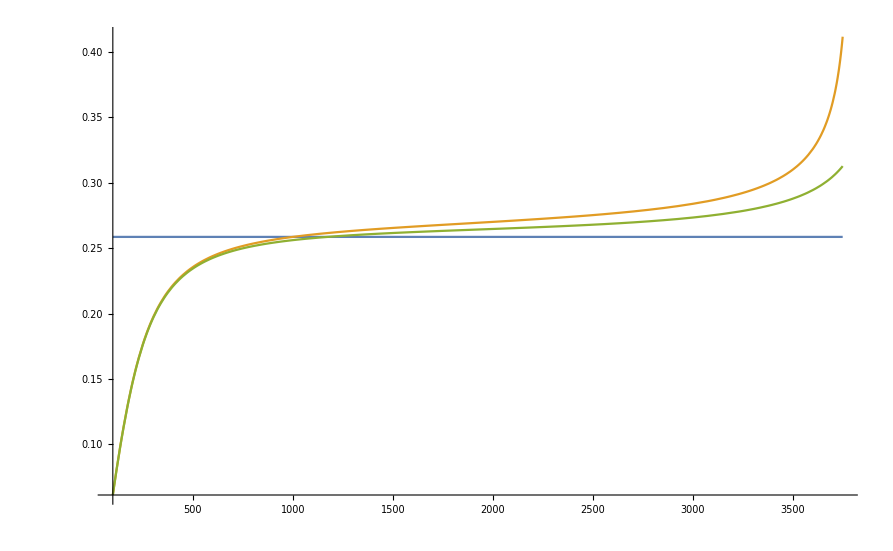

```mathematica
Plot[{kB*3,Evaluate[-x*D[D[Interpolation[Transpose[{tlistall,mine0all}]][x],x],x]],Evaluate[-x*D[D[Interpolation[Transpose[{tlistall,mine0allanh}]][x],x],x]]},{x,100,3750},PlotRange->All]
```

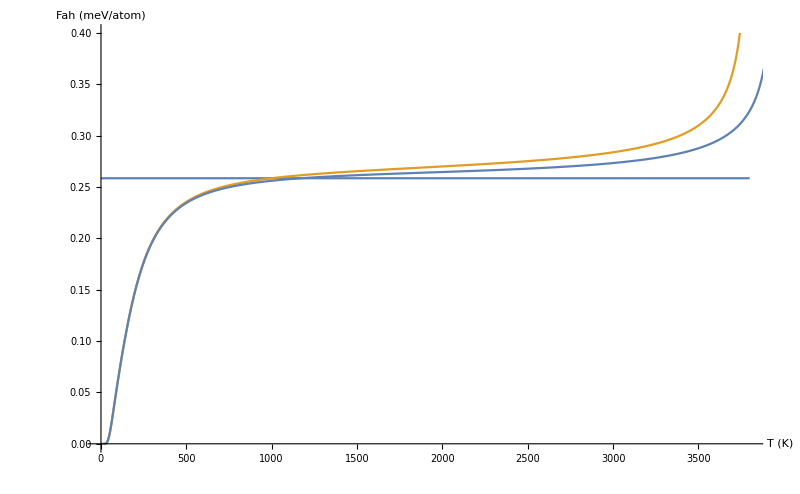

```mathematica
minty=1;
maxty1=3800;
maxty2=3950;
Show[Plot[{kB*3,Evaluate[-x*D[D[Interpolation[Transpose[{tlistall,mine0all}]][x],x],x]]},{x,minty,maxty1},PlotRange->{{minty,maxty1},{0.00,0.4}},AxesLabel->{"T (K)","Fah (meV/atom)"}],
Plot[{Evaluate[-x*D[D[Interpolation[Transpose[{tlistall,mine0allanh}]][x],x],x]]},{x,minty,maxty2},PlotRange->{{minty,maxty2},{0.00,0.4}}],ImageSize->800]
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/output_qha_700eV_666kp/QHA_PERF"];
qhaCp=ReadList["Cp-temperature.dat",{Number, Number}];
```

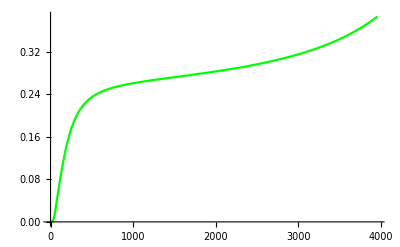

```mathematica
cpQHAnnormal=ListLinePlot[Transpose[{Transpose[qhaCp][[1]],kjmol2evatom*Transpose[qhaCp][[2]]}],PlotStyle->Green]
```

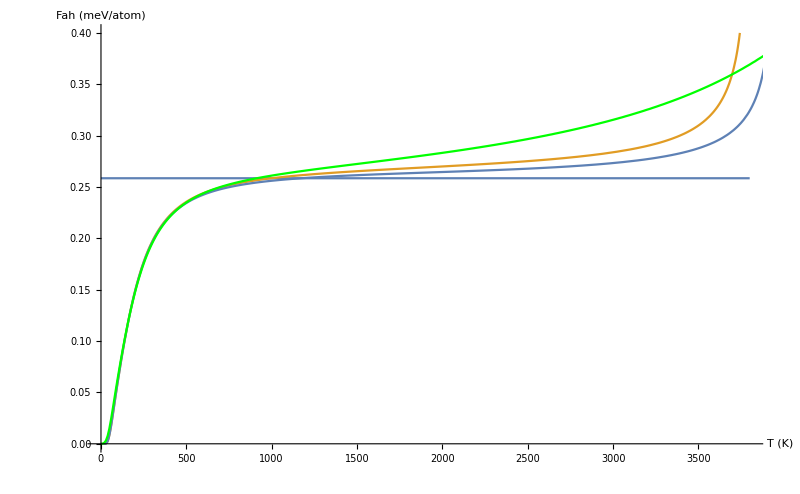

```mathematica
Show[Plot[{kB*3,Evaluate[-x*D[D[Interpolation[Transpose[{tlistall,mine0all}]][x],x],x]]},{x,minty,maxty1},PlotRange->{{minty,maxty1},{0.00,0.4}},AxesLabel->{"T (K)","Fah (meV/atom)"}],
Plot[{Evaluate[-x*D[D[Interpolation[Transpose[{tlistall,mine0allanh}]][x],x],x]]},{x,minty,maxty2},PlotRange->{{minty,maxty2},{0.00,0.4}}],cpQHAnnormal,ImageSize->800]
```